```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=False;
fps=0;

(*Init*)
dir=gFunc@@iterParams;
err=eFunc@@iterParams;

(** Adaptivity **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
(* Running average *)
Smoothness=2;
(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyLength=0;
historyLengthi=0;
historyAmt=300;

(*Display*)
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[q_,samplingRate_,paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(* Data Generation Settings *)
SamplingSet=N[Range[dataLength]]/N[samplingRate];
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];

(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;

(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions *)
eFunc=paramh/._[vars__]:>Function[{vars},N[
Mean[((((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Mean[(Fitfunction@@Prepend[{vars},#])&/@SamplingSet])(Data-Mean[Data]))^2]
]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;

(** Modification Values **)
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
err=-1;
prevErr=-2;
ConsecRefines=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams=If[historyLength>0,ConstantArray[iterParams,historyLength],{iterParams}];
err=eFunc @@ iterParams;
dir=gFunc@@iterParams;
);
LinePlot[points_, size_,amount_]:=Show[
ListPointPlot3D[
{If[amount>0&&size>amount,points[[-amount;;-1]],points]},
PlotRange->All,ImageSize->Medium],
Graphics3D@Line@points
];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nnorm:",norm,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
Visualize[]:=Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]
,If[doPoint,If[varamt==3,If[doGraph,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
LinePlot[debugParams,totalIter,historyAmt]],
"Non-3 dimensions"],
"Disabled"],
If[doEPlot,ListLogPlot[{((eFunc@@#)&)/@debugParams},ImageSize->Medium],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,-factor*Mean[dirs]}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{(Mean[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(dataLength-varamt))^0.5,prevErr}}
},Frame->All,ItemSize->30]];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
RefineFactor[]:=(factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=boostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
```

```mathematica
(* Visualization of the first 3 function parameters *)
varamt=3;
dataLength=100;
Fitfunction=#3*Sin[#1*#2]+#4&;
InitIterationSettings[];
InitFunctionData[0,40,3,{-2.,-1.,0.2},0.01,NormalDistribution[]];
InitIterationData[0.01,{-2.,1.,-2.}];
Visualize[]

Clear[boostvserror]
```

```mathematica
(* Isolation Box *)
InitIterationData[0.01,{0.2,2.,-2.}]
recordAtIter=200;
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0.;UpperBound=100;
SmallErr=0.0000000000000001;
NoErr=True;
Forever=Trie;
ConsecRefines=0;
err=eFunc @@ iterParams;

(* Iteration *)
While[Forever||(i<UpperBound &&(NoErr|| ((err(err-prevErr))^2+1)^2>(1+SmallErr))),
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];
If[ConsecRefines>maxRefines,If[doWarn,Print["Exceeded maximum amount of consecutive corrections."]];Abort[];,RefineFactor[];];,BoostFactor[];];
(* Obtain vector from gradient and assign into running array *)
dirX=Mod[++dirX,Smoothness];dirs[[dirX+1]]=dir=gFunc @@ iterParams;
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[historyLength>0,
historyLengthi=Mod[++historyLengthi,historyLength];
debugParams[[historyLengthi+1]]=iterParams,
debugParams=Append[debugParams,iterParams];
];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*Mean[dirs];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
]
```

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

$Aborted

$Aborted

{0.0164084,-39.6778,1.08376}

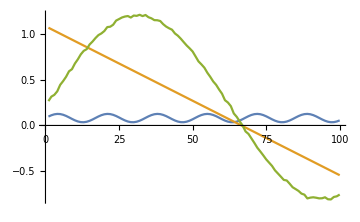

66.9118

```mathematica
(***Diagnostic Tools***)

(*Optional Noise Function Plot*)
Plot[Noise[x],{x,0,40},AspectRatio->Full,ColorFunction->Function[{x,y},Hue[Abs[y-x]]]];

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]]

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet),
((Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet),
Data
},Joined->True,ImageSize->Medium]

Norm[dir]
Style["", 90]
```

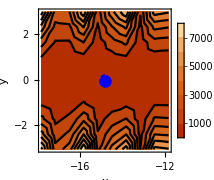
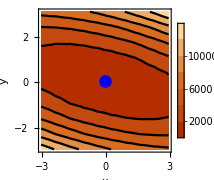
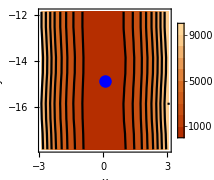

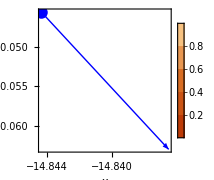
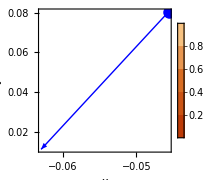
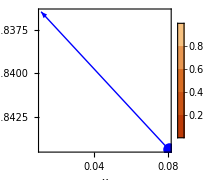

```mathematica
dispGradientRange=3.;
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
{displayGradientNorm[1,2,2.],displayGradientNorm[2,3,2.],displayGradientNorm[3,1,2.]}
```

```mathematica
factor=0.05
```

0.05

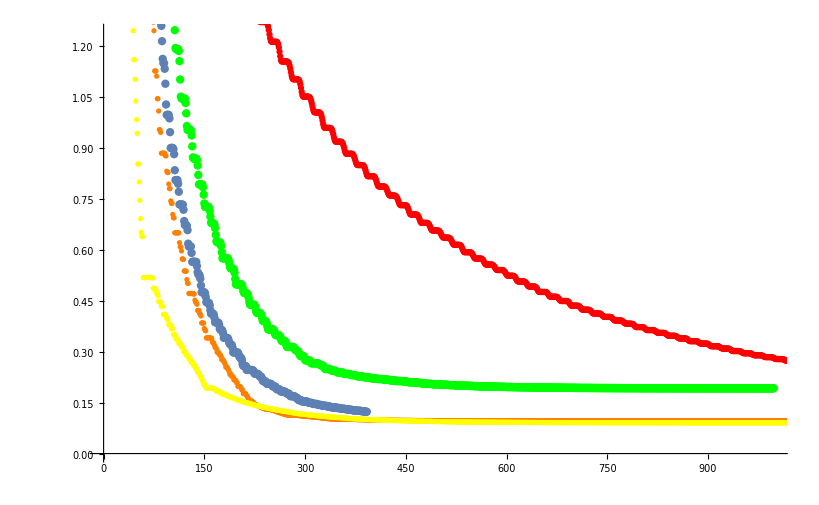

```mathematica
sm2=ListPlot[((eFunc @@ #)&)/@debugParams,PlotStyle->Yellow];
Show[{sm12,sm16,sm4,sm8,sm2},Range->All]
(* Smoothness vs Error convergence *)
```

```mathematica
LinePlot[debugParams,Length[debugParams],100]
```

-Graphics3D-

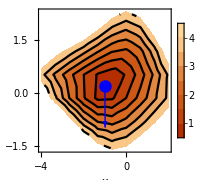

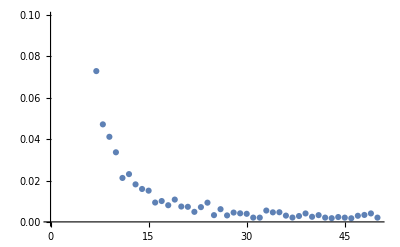

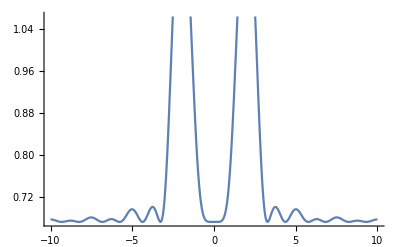

```mathematica
Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {2->x,3->y}]],
{x,iterParams[[2]]-dispGradientRange,iterParams[[2]]+dispGradientRange},{y,iterParams[[3]]-dispGradientRange,iterParams[[3]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤4],
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[2]],iterParams[[3]]}],
Arrow[{{iterParams[[2]],iterParams[[3]]},{iterParams[[2]]-factor*dir[[3]],iterParams[[2]]-factor*dir[[3]]}}]
}]
]
ListPlot[
Abs[((#[[1;;Length[#]/2]])&)/@{Fourier[Data]}]^2
]
Plot[Norm[gFunc[x,0.,0.]],{x,-10,10}]
```

```mathematica
Style["Least Squares Objective Function minimizes χ-squared",90]
```

Least Squares Objective Function minimizes χ-squared